```mathematica
Tn[f_,{a_,b_,m_}]:=0.5*((b-a)/m)*(f[a]+f[b]+Sum[2*f[a+(i*(b-a))/m],{i,1,m-1}])
```

```mathematica
ρ={x*(x-1)*y*(y-1),x^2*(x-1)*y*(y-1),x*(x-1)*y^2*(y-1),x^2*(x-1)*y^2*(y-1)}
```

{(-1+x) x (-1+y) y,(-1+x) x^2 (-1+y) y,(-1+x) x (-1+y) y^2,(-1+x) x^2 (-1+y) y^2}

```mathematica
ϕ=Table[x^i*(x-1),{i,1,3}]
```

{(-1+x) x,(-1+x) x^2,(-1+x) x^3}

```mathematica
Tn[#&,{0,1,100}]
```

0.5

```mathematica
Integrate[x,{x,0,1}]
```

1/2

```mathematica
Tn[#&,{0,20,100}]
```

200.

```mathematica
Integrate[x,{x,0,20}]
```

200

```mathematica
ϕ[[1]]
```

(-1+x) x

```mathematica
ϕ[[2]]
```

(-1+x) x^2

```mathematica
K=Table[Integrate[D[ϕ[[i]],x]*D[ϕ[[j]],x]+ϕ[[i]]*ϕ[[j]],{x,0,1}],{i,3},{j,3}]
```

{{11/30,11/60,23/210},{11/60,1/7,89/840},{23/210,89/840,113/1260}}

```mathematica
F=Table[Integrate[x*ϕ[[i]],{x,0,1}],{i,1,3}]
```

{-1/12,-1/20,-1/30}

```mathematica
LinearSolve[K,F]
```

{-14427/96406,-6944/48203,-21/1121}

```mathematica
Uh[x_]:={-14427/96406,-6944/48203,-21/1121}.{(-1+x) x,(-1+x) x^2,(-1+x) x^3}
```

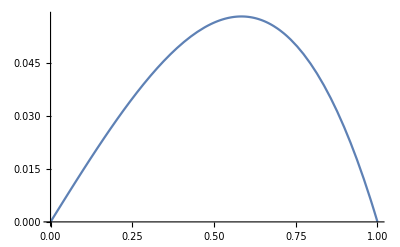

```mathematica
Plot[Uh[x],{x,0,1}]
```

```mathematica
{-14427/96406,-6944/48203,-21/1121}.{(-1+x) x,(-1+x) x^2,(-1+x) x^3}
```

-(14427 (-1+x) x)/96406-(6944 (-1+x) x^2)/48203-(21 (-1+x) x^3)/1121

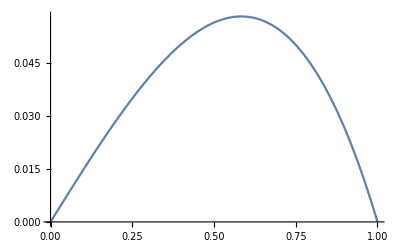

```mathematica
Plot[x-Sinh[x]/Sinh[1],{x,0,1}]
```

```mathematica
Tn[#^2+#+3#&,{0,20,100}]
```

3466.8

```mathematica
K3=Table[D[ϕ[[i]],x]*D[ϕ[[j]],x]+ϕ[[i]]*ϕ[[j]],{i,3},{j,3}]
```

{{(-1+x)^2 x^2+(-1+2 x)^2,(-1+x)^2 x^3+(-1+2 x) (2 (-1+x) x+x^2),(-1+x)^2 x^4+(-1+2 x) (3 (-1+x) x^2+x^3)},{(-1+x)^2 x^3+(-1+2 x) (2 (-1+x) x+x^2),(-1+x)^2 x^4+(2 (-1+x) x+x^2)^2,(-1+x)^2 x^5+(2 (-1+x) x+x^2) (3 (-1+x) x^2+x^3)},{(-1+x)^2 x^4+(-1+2 x) (3 (-1+x) x^2+x^3),(-1+x)^2 x^5+(2 (-1+x) x+x^2) (3 (-1+x) x^2+x^3),(-1+x)^2 x^6+(3 (-1+x) x^2+x^3)^2}}